```mathematica
s1[s_,a_]:=(1/(1-(1+a)^(1-s)))( 1/(1^s)-(1+a)/((1+a)^s) )
s2[s_,a_,c_]:=(( 1/(c^s)-(1+a)/((c(1+a))^s) ))/a
```

```mathematica
Expand[s2[s,tt=.0001,3]/tt]
```

10000. 3^-s-10001. 3.0003^-s

```mathematica
FullSimplify[(1/(1-(1+a)^(1-s)))( 1/(1^s)-(1+a)/((1+a)^s) )]
```

1

```mathematica
s1[s,a]
```

1

```mathematica
FullSimplify[s2[s,a]]
```

2^-s (1-(1+a)^(1-s))

```mathematica
Limit[s2[s,a,2],{a->0}]
```

{2^-s (-1+s)}

```mathematica
Expand[(1/(1-(1+a)^(1-s)))]
```

1/(1-(1+a)^(1-s))

```mathematica
s3[s_,a_]:=(1-(1+a)^(1-s))Zeta[s]/a
```

```mathematica
s3[2,.00001]
```

1.64492

```mathematica
Limit[s3[s,a],{a->0}]
```

{(-1+s) Zeta[s]}

```mathematica
s4[s_,a_]:=(1-(1+a)^(1-s))/(s-1)/a Zeta[s]
s5[s_,a_]:=((s-1)a)/(1-(1+a)^(1-s)) Zeta[s]
```

```mathematica
Limit[s4[s,a],{a->0}]
```

{Zeta[s]}

```mathematica
Limit[s5[s,a],{a->0}]
```

{Zeta[s]}

```mathematica
FullSimplify[(1-(1+a)^(1-s))/(s-1)/a]
```

```mathematica
Limit[(1-(1+a)^(1-s))/(a (-1+s)),a->0]
```

1

```mathematica
f[a_,s_]:=(1-(1+a)^(1-s))/(a (-1+s))
```

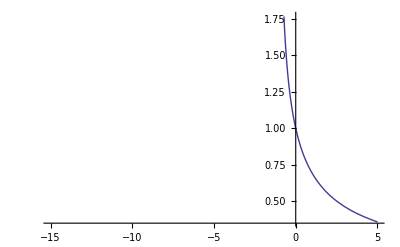

```mathematica
Plot[f[a,.999],{a,-15,5}]
```